# LISSAFIRE: Lissajous-figure Reconstruction for nonlinear polarization tomography of bichromatic fields - Usage and examples

© Emilio Pisanty 2019. Licensed under GPL and CC-BY-SA.

### Readme

LISSAFIRE is a Mathematica package for reconstructing the polarization Lissajous figures of bichromatic ω:2ω light-beam combinations, as described in the paper

 • Knotting fractional-order knots with the polarization state of light. E. Pisanty et al. Nature Photonics, in press (2019), arXiv:1808.05193.

This file provides documentation on the usage of the different functions of the package as well as some benchmarking.

## Usage and Examples

### Loading the package

To load this package, please ensure that a copy of the package file is on the same location as your usage notebook, and run the command

```mathematica
Needs["LISSAFIRE`",FileNameJoin[{NotebookDirectory[],"LISSAFIRE.m"}]]
```

DistributeDefinitions::ctx: No context matching LISSAFIRE` found.

The package can also be called from some  separate directory, by suitably modifying the second argument above.

For longer-term usage, it is more convenient to fully install the package, which can be done by placing a copy of LISSAFIRE.m (or a soft link to that file) in your Mathematica applications directory, $UserBaseDirectory/Applications/. In that case, the package can simply be called via

```mathematica
Needs["LISSAFIRE`"]
```

or even more simply

```mathematica
<<LISSAFIRE`
```

NOTE: At loading time, the package performs on-the-fly a number of symbolic calculations, which means that the package loading takes a brief but noticeable time to run.

To print the version of the package in use, use the command

```mathematica
$LISSAFIREversion
```

LISSAFIRE v1.0.1, Tue 23 Apr 2019 12:35:37

There are also commands to get the $LISSAFIREtimestamp directly, as well as the git $LISSAFIREcommit hash and message.

```mathematica
Quit
```

### Usage messages of the different package functions

```mathematica
?UnitE
```

UnitE[1] and UnitE[-1] return, respectively, 1/(√2){1,ⅈ} and 1/(√2){1,-ⅈ}.

```mathematica
?EnsureRightCircularFundamental
```

EnsureRightCircularFundamental[{E1p,E1m,E2p,E2m}] ensures that the fundamental has right-circular polarization (i.e. |E1p|>|E1m|) by swapping the input to {E1m*,E1p*,E2m*,E2p*} if necessary.

```mathematica
?PhaseNormalization
```

PhaseNormalization[{E1p,E1m,E2p,E2m}] Normalizes the field phases so that E1p is real and positive, by multiplying by an appropriate factor of ⅇ^(-ⅈ ϕ) on E1 and ⅇ^(-2 ⅈ ϕ) on E2.

```mathematica
?NLPTOutcomes
```

NLPTOutcomes[{ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m}] Calculates the Nonlinear Polarization Tomography outcome functions I_n, as defined in the paper, with the normalization set so that the ℓ>0 components of the paper are given by I_ℓ^paper(θ)=Re(2I_ℓⅇ^(ⅈ ℓ θ)).

NLPTOutcomes[{E1p,E1m,E2p,E2m}] Uses explicit complex amplitudes.

```mathematica
?ReconstructionMimimizationTarget
```

ReconstructionMimimizationTarget[{I0,I1,I2,I3,I4}][ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m] calculates the reconstruction target ∑_(n=0)^4 , i.e. the sum of squares of the nonlinear-polarimetry Fourier coefficients in difference between the given I_n and those reconstructed from the given complex fields.

```mathematica
?ReconstructBicircularFieldList
```

ReconstructBicircularFieldList[{I0,I1,I2,I3,I4}] calculates a list of candidate reconstructed fields (each an Association of the form <|"Fields"→{E_(1+),E_(1-),E_(2+),E_(2-)},"Outcomes"→{I_(0, rec),I_(1, rec),I_(2, rec),I_(3, rec),I_(4, rec)},"√Residual"→r,"Residual"→r^2|>), obtained by minimizing ReconstructionMimimizationTarget over a list of random initial seeds pulled from a box of side 1.

ReconstructBicircularFieldList[{I0,I1,I2,I3,I4},Erange] uses a box of side Erange (which can be a single number, or a list of eight real numbers to be used as the sizes of the boxes for {ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m}) for the initial seeds of the minimization.

ReconstructBicircularFieldList[{I0,I1,I2,I3,I4},Erange,iterations] uses the specified number of iterations.

```mathematica
?ReconstructBicircularField
```

ReconstructBicircularField[{I0,I1,I2,I3,I4}] returns the first element of the corresponding ReconstructBicircularFieldList, using the specified (or default) SortingFunction.

ReconstructBicircularField[{I0,I1,I2,I3,I4},Erange] returns the first element of the corresponding ReconstructBicircularFieldList, using the specified (or default) SortingFunction.

ReconstructBicircularField[{I0,I1,I2,I3,I4},Erange,iterations] returns the first element of the corresponding ReconstructBicircularFieldList, using the specified (or default) SortingFunction.

### The formal expression of the NLPTOutcomes

```mathematica
NLPTOutcomes[{ReE1p,ImE1p,ReE1m,ImE1m,ReE2p,ImE2p,ReE2m,ImE2m}]
```

{ImE1m^4/8+(ImE1m^2 ImE1p^2)/2+ImE1p^4/8+ImE2m^2/4+ImE2p^2/4+(ImE1m^2 ReE1m^2)/4+(ImE1p^2 ReE1m^2)/2+ReE1m^4/8+(ImE1m^2 ReE1p^2)/2+(ImE1p^2 ReE1p^2)/4+(ReE1m^2 ReE1p^2)/2+ReE1p^4/8+ReE2m^2/4+ReE2p^2/4,-(ⅈ ImE1m^2 ImE2m)/(4 √2)+(ⅈ ImE1m ImE1p ImE2m)/(2 √2)-(ⅈ ImE1m ImE1p ImE2p)/(2 √2)+(ⅈ ImE1p^2 ImE2p)/(4 √2)+(ImE1m ImE2m ReE1m)/(2 √2)+(ImE1p ImE2m ReE1m)/(2 √2)+(ImE1p ImE2p ReE1m)/(2 √2)+(ⅈ ImE2m ReE1m^2)/(4 √2)+(ImE1m ImE2m ReE1p)/(2 √2)+(ImE1m ImE2p ReE1p)/(2 √2)+(ImE1p ImE2p ReE1p)/(2 √2)-(ⅈ ImE2m ReE1m ReE1p)/(2 √2)+(ⅈ ImE2p ReE1m ReE1p)/(2 √2)-(ⅈ ImE2p ReE1p^2)/(4 √2)-(ImE1m^2 ReE2m)/(4 √2)-(ImE1m ImE1p ReE2m)/(2 √2)-(ⅈ ImE1m ReE1m ReE2m)/(2 √2)+(ⅈ ImE1p ReE1m ReE2m)/(2 √2)+(ReE1m^2 ReE2m)/(4 √2)+(ⅈ ImE1m ReE1p ReE2m)/(2 √2)+(ReE1m ReE1p ReE2m)/(2 √2)-(ImE1m ImE1p ReE2p)/(2 √2)-(ImE1p^2 ReE2p)/(4 √2)-(ⅈ ImE1p ReE1m ReE2p)/(2 √2)-(ⅈ ImE1m ReE1p ReE2p)/(2 √2)+(ⅈ ImE1p ReE1p ReE2p)/(2 √2)+(ReE1m ReE1p ReE2p)/(2 √2)+(ReE1p^2 ReE2p)/(4 √2),(ImE1m^3 ImE1p)/4+(ImE1m ImE1p^3)/4+(ImE2m ImE2p)/4+1/4 ⅈ ImE1m^2 ImE1p ReE1m+1/4 ⅈ ImE1p^3 ReE1m+1/4 ImE1m ImE1p ReE1m^2+1/4 ⅈ ImE1p ReE1m^3-1/4 ⅈ ImE1m^3 ReE1p-1/4 ⅈ ImE1m ImE1p^2 ReE1p+1/4 ImE1m^2 ReE1m ReE1p+1/4 ImE1p^2 ReE1m ReE1p-1/4 ⅈ ImE1m ReE1m^2 ReE1p+(ReE1m^3 ReE1p)/4+1/4 ImE1m ImE1p ReE1p^2+1/4 ⅈ ImE1p ReE1m ReE1p^2-1/4 ⅈ ImE1m ReE1p^3+(ReE1m ReE1p^3)/4+(ⅈ ImE2p ReE2m)/4-(ⅈ ImE2m ReE2p)/4+(ReE2m ReE2p)/4,(ⅈ ImE1p^2 ImE2m)/(4 √2)-(ⅈ ImE1m^2 ImE2p)/(4 √2)+(ImE1m ImE2p ReE1m)/(2 √2)+(ⅈ ImE2p ReE1m^2)/(4 √2)+(ImE1p ImE2m ReE1p)/(2 √2)-(ⅈ ImE2m ReE1p^2)/(4 √2)-(ImE1p^2 ReE2m)/(4 √2)+(ⅈ ImE1p ReE1p ReE2m)/(2 √2)+(ReE1p^2 ReE2m)/(4 √2)-(ImE1m^2 ReE2p)/(4 √2)-(ⅈ ImE1m ReE1m ReE2p)/(2 √2)+(ReE1m^2 ReE2p)/(4 √2),(ImE1m^2 ImE1p^2)/8+1/4 ⅈ ImE1m ImE1p^2 ReE1m-(ImE1p^2 ReE1m^2)/8-1/4 ⅈ ImE1m^2 ImE1p ReE1p+1/2 ImE1m ImE1p ReE1m ReE1p+1/4 ⅈ ImE1p ReE1m^2 ReE1p-(ImE1m^2 ReE1p^2)/8-1/4 ⅈ ImE1m ReE1m ReE1p^2+(ReE1m^2 ReE1p^2)/8}

### Single-run reconstruction of a randomly-generated field

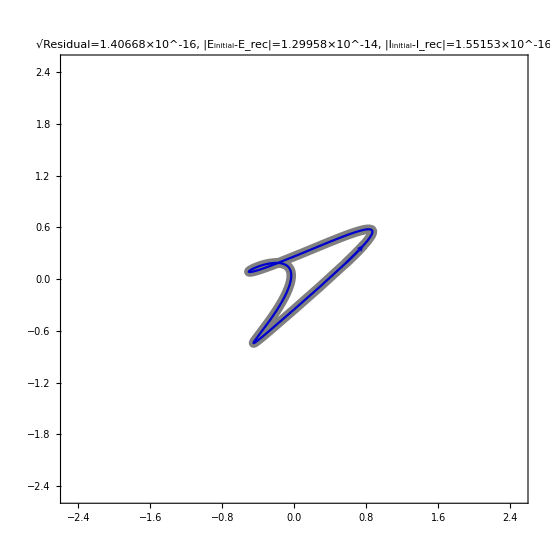

```mathematica
Block[{initialFields,initialValues,solution},

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];

initialValues=NLPTOutcomes[initialFields];

solution=ReconstructBicircularField[initialValues,1,15];


ParametricPlot[{
Evaluate[Tooltip[
(*1.03×*)Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->initialFields
]
,"Initial fields"]],
Evaluate[Tooltip[
Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->solution["Fields"]
]
,"Reconstruction"]]
},{ωt,0,2π}
,PlotStyle->{Directive[Thickness[0.0125],Arrowheads[0.075],GrayLevel[0.5]],Directive[Darker[Blue,0.2]]}
,PlotRange->2.5{{-1,1},{-1,1}}
,PlotPoints->25
,MaxRecursion->2
,Frame->True
,ImageSize->550
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.85]
,PlotLabel->Row[{
"√Residual=",solution["√Residual"],",  ",
"|E_initial-E_rec|=",Norm[initialFields-solution["Fields"]],",  ",
"|I_initial-I_rec|=",Norm[initialValues-NLPTOutcomes[solution["Fields"]]]
}]
]/.{Line[pts_]:>{{Line[pts],Arrow[pts⟦-5;;-1⟧]}}}

]
```

I.e. the blue curve lies completely on top of the gray curve, meaning that (unless the convergence failed, and returned a sub-optimal local minimum, which it can do!) the reconstruction is essentially perfect to within machine accuracy.

### Array of reconstructions over multiple randomly-generated initial fields

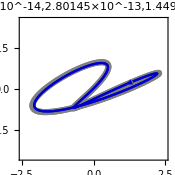
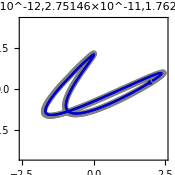
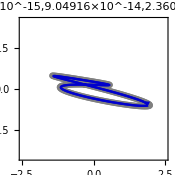
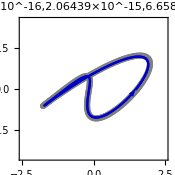
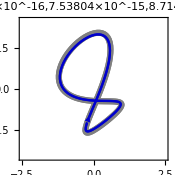
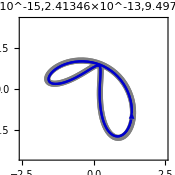
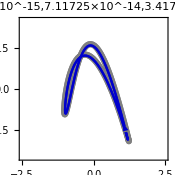
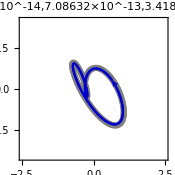

```mathematica
Block[{initialFields,initialValues,solution},

Table[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];
solution=ReconstructBicircularField[initialValues,1,10];

ParametricPlot[{
Evaluate[Tooltip[
1.03×Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->initialFields
]
,"Initial fields"]],
Evaluate[Tooltip[
Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->solution["Fields"]
]
,"Reconstruction"]]
},{ωt,0,2π}
,PlotStyle->{Directive[Thickness[0.025],Arrowheads[0.15],GrayLevel[0.5]],Directive[Arrowheads[0.1],Darker[Blue,0.2]]}
,PlotRange->2.5{{-1,1},{-1,1}}
,PlotPoints->25
,MaxRecursion->2
,Frame->True
,ImageSize->175
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.85]
,PlotLabel->Style[{
solution["√Residual"],
Norm[initialFields-solution["Fields"]],
Norm[initialValues-NLPTOutcomes[solution["Fields"]]]
},FontSize->7]
]/.{Line[pts_]:>{{Line[pts],Arrow[pts]}}}

,{18}]

]
```

### Array of reconstructions over multiple randomly-generated initial fields - with a low iteration number, leading to more errors

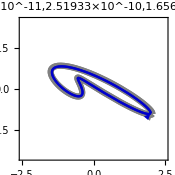
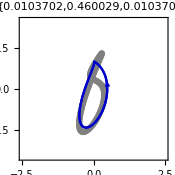
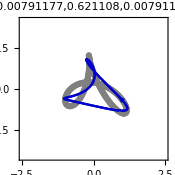
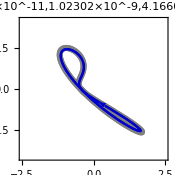
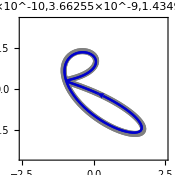
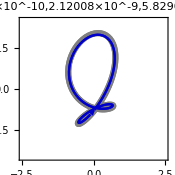
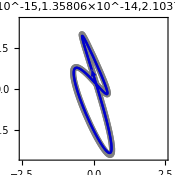
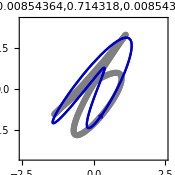

```mathematica
Block[{initialFields,initialValues,solution},

Table[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];
solution=ReconstructBicircularField[initialValues,1,1];

ParametricPlot[{
Evaluate[Tooltip[
1.03×Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->initialFields
]
,"Initial fields"]],
Evaluate[Tooltip[
Re[
(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->solution["Fields"]
]
,"Reconstruction"]]
},{ωt,0,2π}
,PlotStyle->{Directive[Thickness[0.025],Arrowheads[0.15],GrayLevel[0.5]],Directive[Arrowheads[0.1],Darker[Blue,0.2]]}
,PlotRange->2.5{{-1,1},{-1,1}}
,PlotPoints->25
,MaxRecursion->2
,Frame->True
,ImageSize->175
,Method->{"AxesInFront"->False}
,AxesStyle->GrayLevel[0.85]
,PlotLabel->Style[{
solution["√Residual"],
Norm[initialFields-solution["Fields"]],
Norm[initialValues-NLPTOutcomes[solution["Fields"]]]
},FontSize->7]
]/.{Line[pts_]:>{{Line[pts],Arrow[pts]}}}

,{18}]

]
```

### Convergence properties with respect to the iterations number

#### Distribution of error sizes over the iterations for fixed (random) single initial field

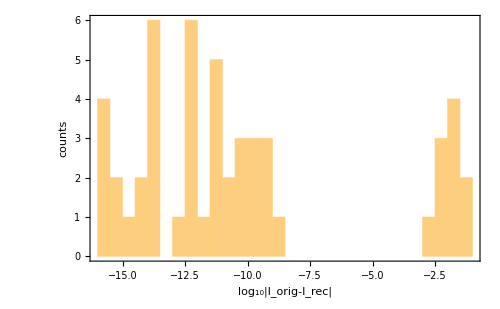

```mathematica
Block[{initialFields,initialValues,solution},
Histogram[
Table[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];

solution=ReconstructBicircularField[initialValues,1,3];

Log10[solution["√Residual"]]

,{50}]
,{0.5}
,Frame->True
,FrameLabel->{"log_10|I_orig-I_rec|","counts"}
,ImageSize->500
]

]
```

This implies that the error is either quite large (with |I_orig-I_rec| of the order of a few percent) or it is very small, with the √residual rather smaller than 10^-10. 

That then implies that it is relatively simple to divide the guesses into successes and failures, by setting up a suitable cut point at some point in that large gap - below we set it at  log_10|I_orig-I_rec|=-7.

#### Convergence testing

The code below runs the reconstruction algorithm at increasing iteration numbers, and then counts the successes and failures at each number of iterations.

Sun 17 Mar 2019 03:45:25

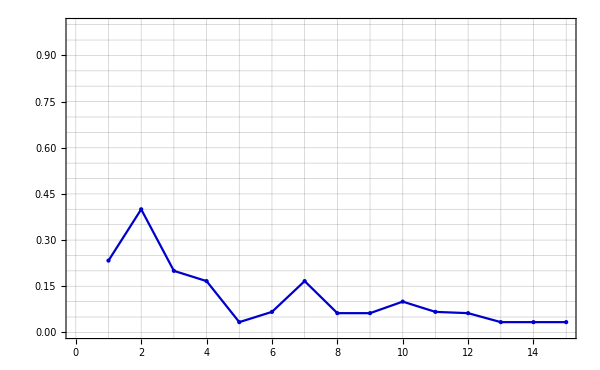
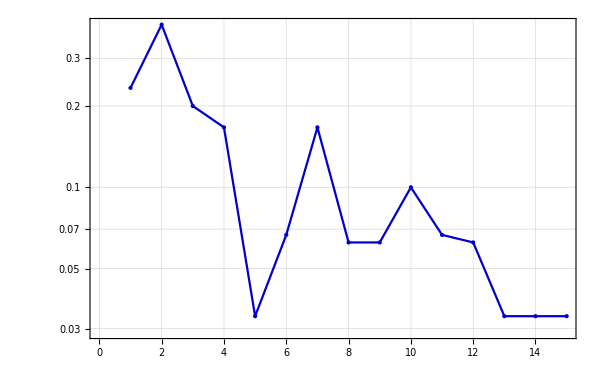

Sun 17 Mar 2019 03:47:46

```mathematica
DateString[]
Block[{initialFields,initialValues,solution,runsPerIterations,maxIterations},
runsPerIterations=30(*1000*);
maxIterations=15(*24*);
convergenceTestData=Table[
{iterations,N[Length[#[True]]/(Length[#[False]]+Length[#[True]])]}&[
GroupBy[
ParallelTable[

initialFields=PhaseNormalization[EnsureRightCircularFundamental[RandomComplex[{-1-ⅈ,1+ⅈ},4]]];
initialValues=NLPTOutcomes[initialFields];

solution=Quiet[
ReconstructBicircularField[initialValues,1,iterations]
,{FindMinimum::cvmit,FindMinimum::sszero}];

Log10[solution["√Residual"]]

,{runsPerIterations}]
,#>-7&
]
]
,{iterations,1,maxIterations}
];
Row[{
ListPlot[
convergenceTestData
,PlotStyle->Directive[PointSize[Large],Darker[Blue,0.2]]
,Frame->True
,GridLines->All
,ImageSize->600
,PlotRange->{0,1}
]/.{Point[pts_]:>{Point[pts],Line[pts]}},
ListLogPlot[
convergenceTestData
,PlotStyle->Directive[PointSize[Large],Darker[Blue,0.2]]
,Frame->True
,GridLines->All
,ImageSize->600
]/.{Point[pts_]:>{Point[pts],Line[pts]}}
}]
]
DateString[]
```

The result is clearly exponential, which means that the error rate goes down exponentially with the iterations number (as would be expected). This then lets us fit the convergence data to a model, to quantify the failure rate per iteration.

#### Quantifying the failure rate

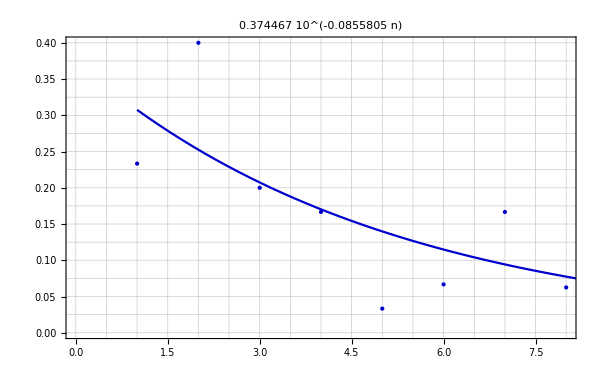

```mathematica
Block[{model},
model=NonlinearModelFit[convergenceTestData⟦1;;10⟧,A 10^(-n/R),{A,R},{n}];
Show[{
ListPlot[
convergenceTestData⟦1;;8(*10*)⟧
,PlotStyle->Directive[PointSize[Large],Darker[Blue,0.2]]
,Frame->True
,GridLines->All
,ImageSize->600
,PlotLabel->model[n]
],
Plot[
model[n]
,{n,1,10}
,PlotStyle->Directive[Darker[Blue,0.2]]
]
}]
]
```

i.e., we have

```mathematica
NonlinearModelFit[convergenceTestData⟦1;;10⟧,A 10^(-n/R),{A,R},{n}]["BestFitParameters"]
```

{A→0.374467,R→11.6849}

or, in other words, about a factor-of-ten decrease in the error rate for every additional R=11 iterations, with a failure rate of 3.7% at n=11 iterations.

### With sample experimental data

#### Loading the sample data

Sample data from the experiment, as described in the paper (Nature Photonics, in press). For the details of how this Fourier-transformed data was calculated from the experimental observations, see the implementation of the paper, available at https://doi.org/10.5281/zenodo.1345139.

```mathematica
Dimensions[Get[FileNameJoin[{NotebookDirectory[],"SampleData","SampleFourierData.txt"}]]]
```

{35,35,5}

#### The various candidate reconstructed fields for a given set of experimental outcomes

As shown above, if the nonlinear polarization tomography outcomes I_n are calculated in a mathematically-exact way from a given set of fields, there is one unique global minimum (modulo the unavoidable indeterminacy of the problem) at a residue which is essentially zero (i.e. at the level of the machine accuracy), and which perfectly reconstructs the initial given fields. For this case there are also other local minima with a higher residue, but if the algorithm is run enough times, it will find the global minimum.

In the presence of noise, however, this is generally no longer the case, and the desired minimum may no longer be the global minimum (at least, with the simplest, naive choice of euclidean distance on the space of the I_n to be minimized over). This means that, in general, ReconstructBicircularFieldList will find multiple valid candidate reconstruction fields, and the one with the minimal √residue (as calculated here) need not be the correct one. To find the right choice, one needs to compare and contrast with the other information known about the experiment (including the known polarizations and spatial distributions of the different drivers in isolation). A full and conclusive analysis requires more input data than what this algorithm uses (and beyond the data that was collected for the first publication, whose main focus was the observation of a nontrivial phase winding in the T_(3,3)(r) field tensor moment). Nevertheless, if used judiciously, the algorithm implemented here is still sufficient to extract a tentative reconstruction of the electromagnetic fields that produced the sample data included here.

Below is a visualization of the different fields produced by ReconstructBicircularFieldList

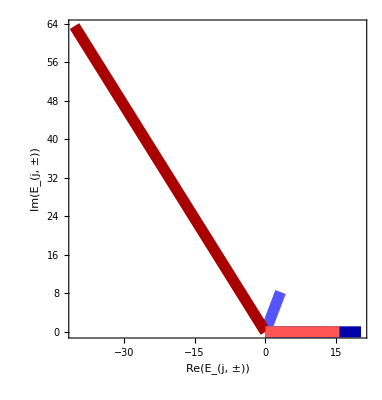
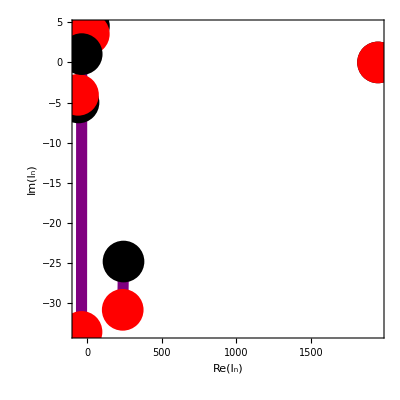
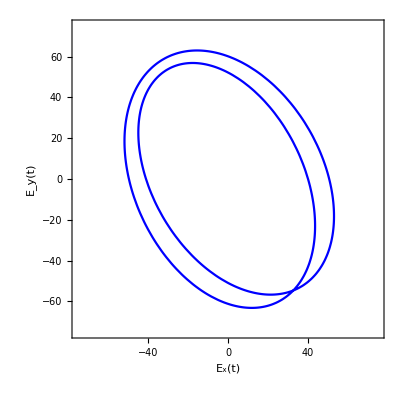
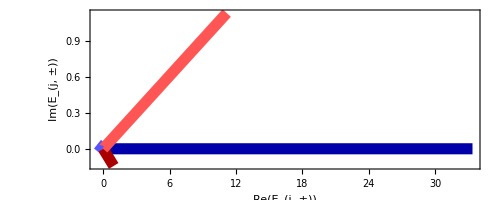
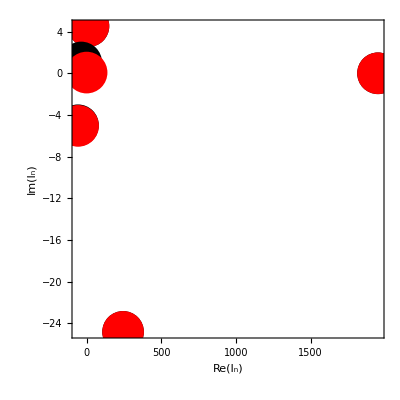
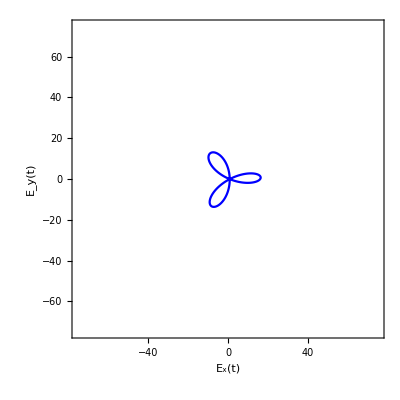
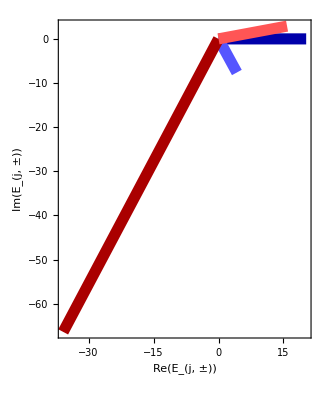
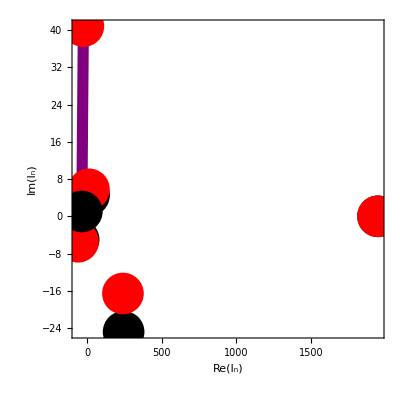
√Residual=35.7846
I_(n, rec)={1949.89,11.9552+3.53902 ⅈ,-60.5882-4.04132 ⅈ,239.157-30.8524 ⅈ,-36.9944-33.6035 ⅈ}
E_(j, ±,rec)={6.75264,1.06721+2.76215 ⅈ,-40.458+63.5511 ⅈ,15.6938+0.0125303 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.677435,0.916818,0.621085}
-Graphics--Graphics--Graphics- | √Residual=36.2569
I_(n, rec)={1950.07,12.6792+4.52851 ⅈ,-56.5134-5.04863 ⅈ,244.435-24.8293 ⅈ,0.4532+0.067512 ⅈ}
E_(j, ±,rec)={11.1276,-0.171587+0.0127103 ⅈ,0.948007-0.143472 ⅈ,11.1668+1.13433 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.999522,-0.985512,-0.985041}
-Graphics--Graphics--Graphics-
√Residual=42.4608
I_(n, rec)={1949.85,11.9696+5.80072 ⅈ,-61.3294-5.46642 ⅈ,239.952-16.585 ⅈ,-25.3438+40.8512 ⅈ}
E_(j, ±,rec)={6.75082,1.41246-2.53848 ⅈ,-35.8844-66.4033 ⅈ,15.8326+2.89443 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.687519,0.913015,0.627714}
-Graphics--Graphics--Graphics- | √Residual=90.9609
I_(n, rec)={1949.92,15.6834+4.49968 ⅈ,-48.0817-5.12452 ⅈ,226.738-24.0946 ⅈ,52.6206-6.33837 ⅈ}
E_(j, ±,rec)={6.93078,-2.96568-0.177971 ⅈ,74.7141+2.15643 ⅈ,13.0233+1.589 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.689535,0.940221,0.648315}
-Graphics--Graphics--Graphics-
√Residual=106.645
I_(n, rec)={1942.28,28.1539-5.08385 ⅈ,-54.2349-18.4688 ⅈ,248.727-42.9134 ⅈ,-100.728-77.8966 ⅈ}
E_(j, ±,rec)={6.73474,-1.53179-4.48473 ⅈ,19.8637-36.9583 ⅈ,49.997+13.8118 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.337643,-0.208941,-0.0705474}
-Graphics--Graphics--Graphics- | √Residual=114.014
I_(n, rec)={1941.81,31.2421+14.8994 ⅈ,-52.4768+8.84009 ⅈ,251.774-4.83506 ⅈ,-84.2912+98.316 ⅈ}
E_(j, ±,rec)={6.74072,-1.99503+4.33832 ⅈ,17.4811+37.7577 ⅈ,51.4396-5.07083 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.331721,-0.213608,-0.0708581}
-Graphics--Graphics--Graphics-

```mathematica
Block[{m=2,x,y,targetData,reconstructions,fields,fieldDuplicateTolerance=1.,F1=1,F2=1,imagesize=190},

x=10;
y=18;

targetData=sampleData⟦x,y⟧;


reconstructions=DeleteDuplicates[
SortBy[
ReconstructBicircularFieldList[
targetData,
50(*{1,1,0,0,0,0,1,1}*),
100,
Parallelize->True,
SortingFunction->Function[#["Residual"]],
SelectionFunction->Function[True]
],
#["Residual"]&
],
Function[
Norm[#1["Fields"]-#2["Fields"]]<fieldDuplicateTolerance
]
];


Grid[
Partition[
Table[
Column[{
Row[{"√Residual=",entry["√Residual"]}],
Row[{"I_(n, rec)=",entry["Outcomes"]}],
Row[{"E_(j, ±,rec)=",entry["Fields"]}],
Function[{E1p,E1m,E2p,E2m},
Row[{"{ϵ_1,ϵ_2,ϵ_1ϵ_2}=",
{(Abs[E1p]^2-Abs[E1m]^2)/Norm[{E1p,E1m}]^2,(Abs[E2p]^2-Abs[E2m]^2)/Norm[{E2p,E2m}]^2,(Abs[E1p]^2-Abs[E1m]^2)/Norm[{E1p,E1m}]^2(Abs[E2p]^2-Abs[E2m]^2)/Norm[{E2p,E2m}]^2}
}]
]@@entry["Fields"],
Row[{
Show[
Graphics[{
Thickness[0.02],Arrowheads[0.1],
Darker[Blue],Tooltip[Arrow[{{0,0},3ReIm[entry["Fields"]⟦1⟧]}],"E_(1, +)"],
Lighter[Blue],Tooltip[Arrow[{{0,0},3ReIm[entry["Fields"]⟦2⟧]}],"E_(1, -)"],
Darker[Red],Tooltip[Arrow[{{0,0},ReIm[entry["Fields"]⟦3⟧]}],"E_(2, +)"],
Lighter[Red],Tooltip[Arrow[{{0,0},ReIm[entry["Fields"]⟦4⟧]}],"E_(2, -)"]
}]
,PlotStyle->Directive[PointSize[Large]]
,ImageSize->imagesize{{1},{1}}
,Frame->True
,AspectRatio->Automatic
,PlotRangePadding->Scaled[.09]
,FrameLabel->{"Re(E_(j, ±))","Im(E_(j, ±))"}
],
Show[
Table[
Graphics[

{
PointSize[0.075],Thickness[0.02],
Purple,Tooltip[Line[{ReIm[targetData⟦n+1⟧],ReIm[entry["Outcomes"]⟦n+1⟧]}],"\!\(\*SubscriptBox[\(I\), \("<>ToString[n]<>"\)]\)"],
Black,Tooltip[Point[ReIm[targetData⟦n+1⟧]],"\!\(\*SubscriptBox[\(I\), \("<>ToString[n]<>",orig\)]\)"],
Red,Tooltip[Point[ReIm[entry["Outcomes"]]⟦n+1⟧],"\!\(\*SubscriptBox[\(I\), \("<>ToString[n]<>",rec\)]\)"]
}

]
,{n,0,4}]
,PlotStyle->Directive[PointSize[Large]]
,ImageSize->imagesize{{1},{1}}
,Frame->True
,AspectRatio->1
,PlotRangePadding->Scaled[.09]
,FrameLabel->{"Re(I_n)","Im(I_n)"}
]
,
ParametricPlot[
Evaluate[{
(*Re[
F1(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+0.05F2(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->entry["Fields"]
],*)
Re[
F1(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+F2(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->entry["Fields"]
]
}],{ωt,0,2π}
,PlotStyle->{(*Gray,*)Blue}
,PlotRange->75{{-1,1},{-1,1}}
,Frame->True
,ImageSize->imagesize{{1},{1}}
,Method->{"AxesInFront"->False}
,FrameLabel->{"E_x(t)","E_y(t)"}
]
}]
}]
,{entry,reconstructions}]
,2]
]


]
```

#### The various candidate reconstructed fields, with a structured initial box

Most of the candidate reconstructions above are incompatible with the experiment, because they have equal helicities for both of the drivers. The simplest way to guide the reconstruction away from this feature, without going (yet) to the extremes of discarding existing solutions based on external criteria, is to use a structured range for the initial box used in the reconstruction, i.e. to preferentially guide the field reconstruction algorithm to seeds that only contain the left- and right-circular polarizations known to occur in the experiment. This is done by setting the third argument of ReconstructBicircularFieldList to

     Erange=50{1,1,0,0,0,0,1,1},

and it results in a marked improvement in the plausibility of the reconstructions it produces

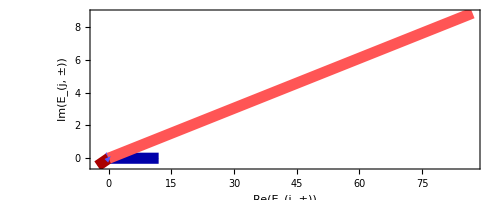
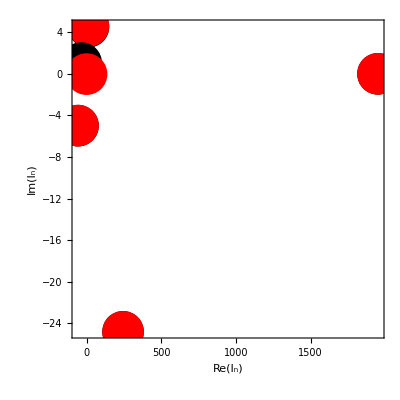
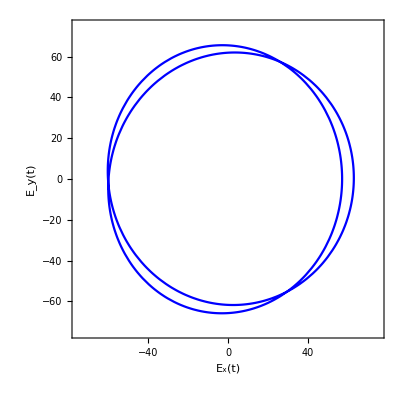
√Residual=35.8505
I_(n, rec)={1950.06,12.572+4.59185 ⅈ,-57.0553-4.98612 ⅈ,244.439-24.8353 ⅈ,0.0479087-0.0282475 ⅈ}
E_(j, ±,rec)={3.98436,0.161508+0.0440686 ⅈ,-2.68973-0.470228 ⅈ,87.1065+8.85138 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.996475,-0.998057,-0.994539}
-Graphics--Graphics--Graphics- | √Residual=36.2569
I_(n, rec)={1950.07,12.6792+4.52851 ⅈ,-56.5134-5.04863 ⅈ,244.435-24.8293 ⅈ,0.4532+0.067512 ⅈ}
E_(j, ±,rec)={11.1276,-0.171587+0.0127103 ⅈ,0.948007-0.143472 ⅈ,11.1668+1.13433 ⅈ}
{ϵ_1,ϵ_2,ϵ_1ϵ_2}={0.999522,-0.985512,-0.985041}
-Graphics--Graphics--Graphics-

```mathematica
Block[{m=2,x,y,targetData,reconstructions,fields,fieldDuplicateTolerance=1.,F1=1,F2=1,imagesize=190},

x=10;
y=18;

targetData=sampleData⟦x,y⟧;


reconstructions=DeleteDuplicates[
SortBy[
ReconstructBicircularFieldList[
targetData,
50{1,1,0,0,0,0,1,1},
300,
Parallelize->True,
SortingFunction->Function[#["Residual"]],
SelectionFunction->Function[True]
],
#["Residual"]&
],
Function[
Norm[#1["Fields"]-#2["Fields"]]<fieldDuplicateTolerance
]
];


Grid[
Partition[
Table[
Column[{
Row[{"√Residual=",entry["√Residual"]}],
Row[{"I_(n, rec)=",entry["Outcomes"]}],
Row[{"E_(j, ±,rec)=",entry["Fields"]}],
Function[{E1p,E1m,E2p,E2m},
Row[{"{ϵ_1,ϵ_2,ϵ_1ϵ_2}=",
{(Abs[E1p]^2-Abs[E1m]^2)/Norm[{E1p,E1m}]^2,(Abs[E2p]^2-Abs[E2m]^2)/Norm[{E2p,E2m}]^2,(Abs[E1p]^2-Abs[E1m]^2)/Norm[{E1p,E1m}]^2(Abs[E2p]^2-Abs[E2m]^2)/Norm[{E2p,E2m}]^2}
}]
]@@entry["Fields"],
Row[{
Show[
Graphics[{
Thickness[0.02],Arrowheads[0.1],
Darker[Blue],Tooltip[Arrow[{{0,0},3ReIm[entry["Fields"]⟦1⟧]}],"E_(1, +)"],
Lighter[Blue],Tooltip[Arrow[{{0,0},3ReIm[entry["Fields"]⟦2⟧]}],"E_(1, -)"],
Darker[Red],Tooltip[Arrow[{{0,0},ReIm[entry["Fields"]⟦3⟧]}],"E_(2, +)"],
Lighter[Red],Tooltip[Arrow[{{0,0},ReIm[entry["Fields"]⟦4⟧]}],"E_(2, -)"]
}]
,PlotStyle->Directive[PointSize[Large]]
,ImageSize->imagesize{{1},{1}}
,Frame->True
,AspectRatio->Automatic
,PlotRangePadding->Scaled[.09]
,FrameLabel->{"Re(E_(j, ±))","Im(E_(j, ±))"}
],
Show[
Table[
Graphics[

{
PointSize[0.075],Thickness[0.02],
Purple,Tooltip[Line[{ReIm[targetData⟦n+1⟧],ReIm[entry["Outcomes"]⟦n+1⟧]}],"\!\(\*SubscriptBox[\(I\), \("<>ToString[n]<>"\)]\)"],
Black,Tooltip[Point[ReIm[targetData⟦n+1⟧]],"\!\(\*SubscriptBox[\(I\), \("<>ToString[n]<>",orig\)]\)"],
Red,Tooltip[Point[ReIm[entry["Outcomes"]]⟦n+1⟧],"\!\(\*SubscriptBox[\(I\), \("<>ToString[n]<>",rec\)]\)"]
}

]
,{n,0,4}]
,PlotStyle->Directive[PointSize[Large]]
,ImageSize->imagesize{{1},{1}}
,Frame->True
,AspectRatio->1
,PlotRangePadding->Scaled[.09]
,FrameLabel->{"Re(I_n)","Im(I_n)"}
]
,
ParametricPlot[
Evaluate[{
(*Re[
F1(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+0.05F2(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->entry["Fields"]
],*)
Re[
F1(E1p UnitE[1]+E1m UnitE[-1])ⅇ^(-ⅈ ωt)+F2(E2p UnitE[1]+E2m UnitE[-1])ⅇ^(-2ⅈ ωt)
]/.Thread[
{E1p,E1m,E2p,E2m}->entry["Fields"]
]
}],{ωt,0,2π}
,PlotStyle->{(*Gray,*)Blue}
,PlotRange->75{{-1,1},{-1,1}}
,Frame->True
,ImageSize->imagesize{{1},{1}}
,Method->{"AxesInFront"->False}
,FrameLabel->{"E_x(t)","E_y(t)"}
]
}]
}]
,{entry,reconstructions}]
,2]
]


]
```

This still tends to produce two different trefoils, with clear differences in how they apportion intensity to the fundamental and its second harmonic. This then provides useful grounds to use the known intensities of the two beams to select the correct solution from within this set.